```mathematica
σlp[p_]:=(8.3145*220*(dN0*(Log[1+K*p/N0]-K*p/N0/(1+K*p/N0))
+dK*p/(1+K*p/N0)))/.{N0-> 9.0,K->50.1,dN0->1.0*^-2,dK->-2.6*^-2}
σnp[p_]:=(8.3145*220*(dN0*(Log[1+K*p/N0]-K*p/N0/(1+K*p/N0))
+dK*p/(1+K*p/N0)))/.{N0-> 2.8,K->778.2,dN0->4.8*^-3,dK->-8.26}
Nlp[p_]:=K*p/(1+K*p/N0)/.{N0-> 9.0,K->50.1}
Nnp[p_]:=K*p/(1+K*p/N0)/.{N0-> 2.8,K->778.2}
```

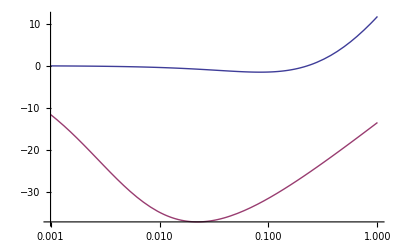

```mathematica
LogLinearPlot[{σlp[p],σnp[p]},{p,0.001,1},PlotStyle->Thick]
```

```mathematica
Manipulate[
LogLinearPlot[{0,σnp[p],σnp[p]/r},{p,0.00001,40},PlotStyle->Thick,PlotRange->All],
{r,1,5}]
```

```mathematica
(* Breathing *)
```

```mathematica
σlp[8.5*^-3]
NSolve[σlp[8.5*^-3]==σlp[p],p]
```

-0.366737

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.0085},{p→0.205604}}

```mathematica
σnp[0.34]
NSolve[σnp[0.34]==σnp[p],p]
```

-22.4529

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.00276979},{p→0.34}}

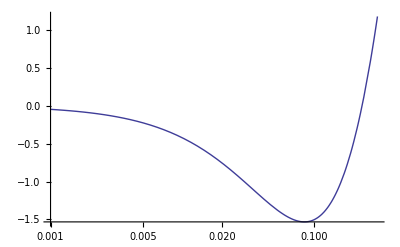

```mathematica
LogLinearPlot[{σlp[p]},{p,0.001,0.3},PlotStyle->Thick]
```

```mathematica
N1[p_]:=If[σlp[p]>-0.3667371747369702,Nlp[p],Nnp[p]]
N2[p_]:=If[σnp[p]<-22.452932250625558,Nnp[p],Nlp[p]]
```

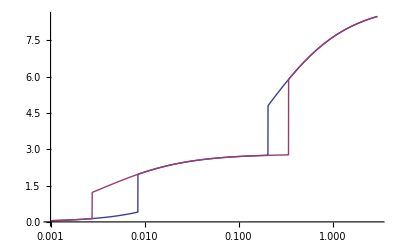

```mathematica
LogLinearPlot[{N1[p],N2[p]},{p,0.001,3},PlotStyle->Thick]
```

```mathematica
(* Supposing the composite affects both phases *)
N1x[p_,r_]:=If[σlp[p]/r>-0.3667371747369702,Nlp[p],Nnp[p]]
N2x[p_,r_]:=If[σnp[p]/r<-22.452932250625558,Nnp[p],Nlp[p]]
```

```mathematica
Manipulate[
LogLinearPlot[{N1x[p,r],N2x[p,r]},{p,0.001,3},PlotStyle->Thick],
{r,1,2}]
```

```mathematica
(* Supposing the composite affects only the lp phase *)
N1x[p_,r_]:=If[σlp[p]/r>-0.3667371747369702,Nlp[p],Nnp[p]]
N2x[p_,r_]:=If[σnp[p]<-22.452932250625558,Nnp[p],Nlp[p]]
```

```mathematica
Manipulate[
LogLinearPlot[{N1x[p,r],N2x[p,r]},{p,0.001,3},PlotStyle->Thick],
{r,1,5}]
```